```mathematica
(* lets generate some random data with an exponential distribution (not normally distributed *)
data=Table[Table[-Log[Random[]],{i,1,k}],{k,2,1000,10}];
meanVals=Table[{Length[data[[i]]],Mean[data[[i]]]},{i,1,Length[data]}];
sdVals=Table[{Length[data[[i]]],StandardDeviation[data[[i]]]},{i,1,Length[data]}];
```

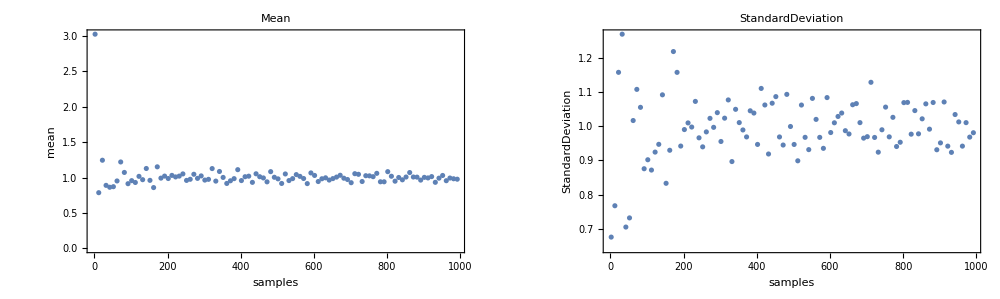

```mathematica
GraphicsGrid[{{
ListPlot[meanVals,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"samples","mean"},PlotLabel->"Mean"],
ListPlot[sdVals,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"samples","StandardDeviation"},PlotLabel->"StandardDeviation"]
}},ImageSize->1000]

(* the average value appears to be getting closer and closer to the mean of μ=1$.  The standard deviation appears to be getting closer to the theoretical value σ=1 *)
```

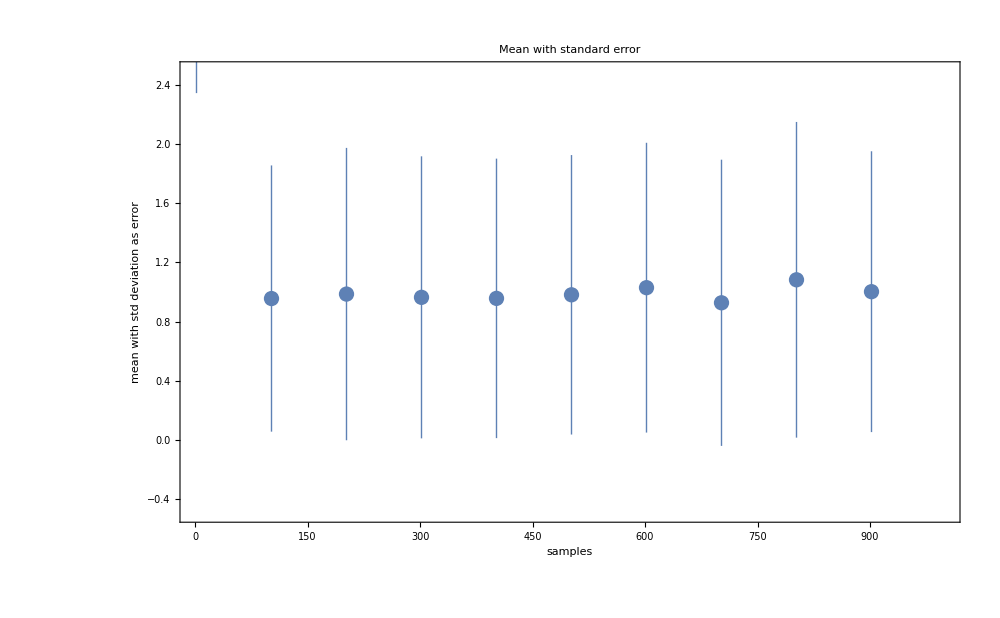

```mathematica
(* Standard deviation is not a useful indicator of the accuracy of the measured average.  *)
ListPlot[Table[{Length[data[[i]]],Around[Mean[data[[i]]],StandardDeviation[data[[i]]]]},{i,1,Length[data],10}],PlotRange->{{0,1000},{-.5,2.5}},Frame->True,Axes->False,FrameLabel->{"samples","mean with std deviation as error"},PlotLabel->"Mean with standard error",ImageSize->1000,BaseStyle->FontSize->20]
```

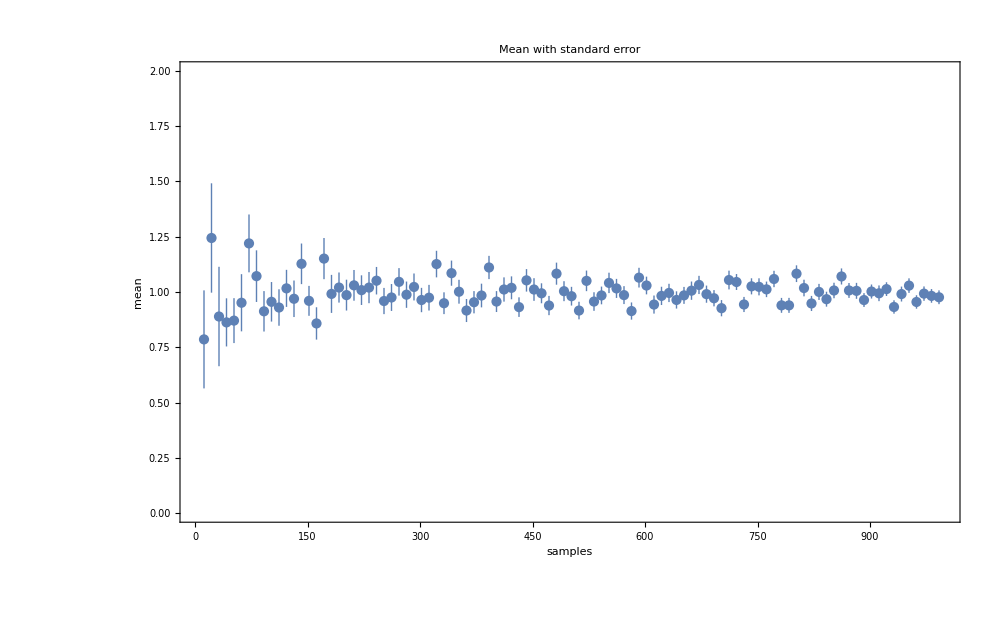

```mathematica
(* Standard deviation is not a useful indicator of the accuracy of the measured average.  *)
ListPlot[Table[{Length[data[[i]]],Around[Mean[data[[i]]],StandardDeviation[data[[i]]]/Sqrt[Length[data[[i]]]]]},{i,1,Length[data],1}],PlotRange->{{0,1000},{0,2}},Frame->True,FrameLabel->{"samples","mean"},PlotLabel->"Mean with standard error",ImageSize->1000,BaseStyle->FontSize->20]
```

```mathematica
(* Standard errors don't overlap in multiple places.  95% confidence interval indicates the region in which there's a 95% chance of finding the average.  

To find the 95% CI, we need to simply integrate a gaussian up to a point y=zσ such that 95% of the area under the curve is between -y to y.  *)
distro=1/Sqrt[2π σ^2]Exp[-x^2/2/σ^2];
area=PowerExpand[Integrate[distro,{x,-z σ,z σ},GenerateConditions->False]];
OptimalLength=FindRoot[area==0.95,{z,1}]
```

{z→1.95996}

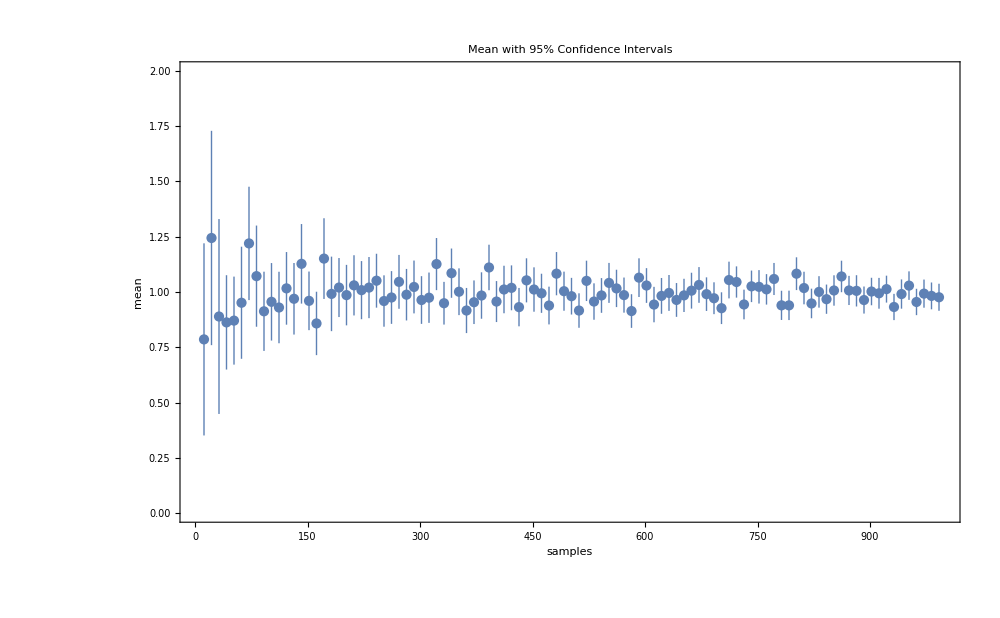

{y→1.95996}

```mathematica
(* so we just multiply by 1.96 to get our new bars *)
ListPlot[Table[{Length[data[[i]]],Around[Mean[data[[i]]],1.96StandardDeviation[data[[i]]]/Sqrt[Length[data[[i]]]]]},{i,1,Length[data],1}],PlotRange->{{0,1000},{0,2}},Frame->True,FrameLabel->{"samples","mean"},PlotLabel->"Mean with 95% Confidence Intervals",ImageSize->1000,BaseStyle->FontSize->20]
```

```mathematica
Erf[100.]
```

1.